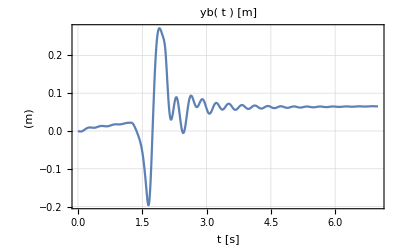

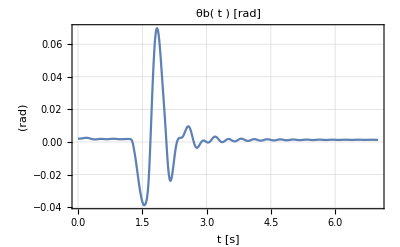

```mathematica
f=OpenRead["D:\OneDrive\Documents\POLI\IC\mecanismo e entradas\dataVz.txt"];
data1=ReadList[f,{Number,Number}];
Close[f];
a=OpenRead["D:\OneDrive\Documents\POLI\IC\mecanismo e entradas\data_Pitch_Angle.txt"];
data3=ReadList[a,{Number,Number}];
Close[a];

(* Deslocamento de dados da velocidade para que a integral (deslocamento) seja mais coerente *)
data2 =Subtract[data1,{{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083},{0,0.039083}}];

data4 = Times[data3, {{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)},{1,((2*Pi)/360)}}];

velocidade1= Interpolation[data1];
vz= Interpolation[data2];
z1[t] = Integrate[velocidade1[t],t];
dz[t] =Integrate[vz[t],t];

angle = Interpolation[data4];

omega[t] = D[angle[t],t];
Plot[dz[t],{t, 0,7}, PlotRange->All, PlotLabel->"yb( t )  [m]", LabelStyle->"Subsubsection", Frame->True, GridLines->Automatic, AxesLabel->{"t [s]","(m)"}]

Plot[angle[t],{t, 0,7}, PlotRange->All, PlotLabel->"θb( t ) [rad]", LabelStyle->"Subsubsection", Frame->True, GridLines->Automatic, AxesLabel->{"t [s]","(rad)"}]
```

```mathematica
d=2;
v=11.11;
hL=0.1;
dL=5;
```

```mathematica
T = 1/2* m1 *( x'[t]^2+ 1/3 L^2 θ'[t]^2) + 1/2*m2*((x'[t]+y'[t]*Cos[θ[t]]-θ'[t]*y[t]*Sin[θ[t]])^2 + (-y'[t]*Sin[θ[t]]-θ'[t]*y[t]*Cos[θ[t]])^2);
V = m1*g *x[t]  + 1/2 k1 ((x[t] + L *Sin[θ[t]] - udir[t] - 0.5)^2 +(L*(1-Cos[θ[t]]))^2) + 1/2 k1 ((x[t] - L *Sin[θ[t]] - uesq[t] - 0.5)^2+(L*(1-Cos[θ[t]]))^2) + m2 * g (x[t]+(y[t]-l)* Cos[θ[t]]) + 1/2 k2 (y[t]- l)^2 ;
R =  1/2 c1* (D[x[t] + L *Sin[θ[t]] - udir[t],t]^2 +D[L*(1-Cos[θ[t]]),t]^2)+ 1/2 c1 *(D[x[t] - L *Sin[θ[t]] - uesq[t],t]^2+D[L*(1-Cos[θ[t]]),t]^2) + 1/2 c2 D[y[t]-l,t]^2;
```

```mathematica
𝕢[t_] = {x[t], y[t], θ[t]};
𝕖[t_] = Flatten @ Solve[(D[D[T,D[#,t]],t]-D[T,#]+D[V,#]+D[R,D[#,t]]==0)& /@ 𝕢[t], 𝕢''[t]]//Simplify;
𝕖[t]//TableForm
```

x''[t]→(1. k1 L^2 m1-1. g L^2 m1^2-0.5 g L^2 m1 m2-1. k2 l L^2 m1 Cos[θ[t]]+0.5 g L^2 m1 m2 Cos[2 θ[t]]-2. k1 L^2 m1 x[t]-3. k1 L^2 m2 y[t]-1.5 g l m2^2 y[t]+1. k2 L^2 m1 Cos[θ[t]] y[t]+3. k1 L^2 m2 Cos[2 θ[t]] y[t]+1.5 g l m2^2 Cos[2 θ[t]] y[t]+3. k1 m2 y[t]^2-3. g m1 m2 y[t]^2-3. k2 l m2 Cos[θ[t]] y[t]^2-6. k1 m2 x[t] y[t]^2+3. k2 m2 Cos[θ[t]] y[t]^3+k1 uesq[t] (1. L^2 m1-1.5 L m2 Sin[2 θ[t]] y[t]+3. m2 y[t]^2)+k1 udir[t] (1. L^2 m1+1.5 L m2 Sin[2 θ[t]] y[t]+3. m2 y[t]^2)+1. c1 L^2 m1 udir'[t]+1.5 c1 L m2 Sin[2 θ[t]] y[t] udir'[t]+3. c1 m2 y[t]^2 udir'[t]+1. c1 L^2 m1 uesq'[t]-1.5 c1 L m2 Sin[2 θ[t]] y[t] uesq'[t]+3. c1 m2 y[t]^2 uesq'[t]-2. c1 L^2 m1 x'[t]-6. c1 m2 y[t]^2 x'[t]+1. c2 L^2 m1 Cos[θ[t]] y'[t]+3. c2 m2 Cos[θ[t]] y[t]^2 y'[t]-6. c1 L^2 m2 Sin[θ[t]] y[t] θ'[t]+2. L^2 m1 m2 Sin[θ[t]] y'[t] θ'[t])/(m1 (L^2 (1. m1+0.5 m2-0.5 m2 Cos[2 θ[t]])+3. m2 y[t]^2))
y''[t]→(1. k2 l L^4 m1^3+1. k2 l L^4 m1^2 m2-1. k1 L^4 m1^2 m2 Cos[θ[t]]+2. k1 L^4 m1^2 m2 Cos[θ[t]] x[t]-1. k2 L^4 m1^3 y[t]-1. k2 L^4 m1^2 m2 y[t]+1.5 k1 L^4 m1 m2^2 Cos[θ[t]] y[t]+0.75 g l L^2 m1 m2^3 Cos[θ[t]] y[t]-1.5 k1 L^4 m1 m2^2 Cos[3 θ[t]] y[t]-0.75 g l L^2 m1 m2^3 Cos[3 θ[t]] y[t]+6. k2 l L^2 m1^2 m2 y[t]^2+4.5 k2 l L^2 m1 m2^2 y[t]^2-6. k1 L^2 m1 m2^2 Cos[θ[t]] y[t]^2+1.5 k2 l L^2 m1 m2^2 Cos[2 θ[t]] y[t]^2+12. k1 L^2 m1 m2^2 Cos[θ[t]] x[t] y[t]^2-6. k2 L^2 m1^2 m2 y[t]^3-4.5 k2 L^2 m1 m2^2 y[t]^3+4.5 k1 L^2 m2^3 Cos[θ[t]] y[t]^3+2.25 g l m2^4 Cos[θ[t]] y[t]^3-1.5 k2 L^2 m1 m2^2 Cos[2 θ[t]] y[t]^3-4.5 k1 L^2 m2^3 Cos[3 θ[t]] y[t]^3-2.25 g l m2^4 Cos[3 θ[t]] y[t]^3+9. k2 l m1 m2^2 y[t]^4+4.5 k2 l m2^3 y[t]^4-9. k1 m2^3 Cos[θ[t]] y[t]^4+4.5 k2 l m2^3 Cos[2 θ[t]] y[t]^4+18. k1 m2^3 Cos[θ[t]] x[t] y[t]^4-9. k2 m1 m2^2 y[t]^5-4.5 k2 m2^3 y[t]^5-4.5 k2 m2^3 Cos[2 θ[t]] y[t]^5+k1 m2 udir[t] (-1. L^4 m1^2 Cos[θ[t]]+L^3 m1 m2 (-0.75 Sin[θ[t]]-0.75 Sin[3 θ[t]]) y[t]-6. L^2 m1 m2 Cos[θ[t]] y[t]^2+L m2^2 (-2.25 Sin[θ[t]]-2.25 Sin[3 θ[t]]) y[t]^3-9. m2^2 Cos[θ[t]] y[t]^4)+k1 m2 uesq[t] (-1. L^4 m1^2 Cos[θ[t]]+L^3 m1 m2 (0.75 Sin[θ[t]]+0.75 Sin[3 θ[t]]) y[t]-6. L^2 m1 m2 Cos[θ[t]] y[t]^2+L m2^2 (2.25 Sin[θ[t]]+2.25 Sin[3 θ[t]]) y[t]^3-9. m2^2 Cos[θ[t]] y[t]^4)-1. c1 L^4 m1^2 m2 Cos[θ[t]] udir'[t]-0.75 c1 L^3 m1 m2^2 Sin[θ[t]] y[t] udir'[t]-0.75 c1 L^3 m1 m2^2 Sin[3 θ[t]] y[t] udir'[t]-6. c1 L^2 m1 m2^2 Cos[θ[t]] y[t]^2 udir'[t]-2.25 c1 L m2^3 Sin[θ[t]] y[t]^3 udir'[t]-2.25 c1 L m2^3 Sin[3 θ[t]] y[t]^3 udir'[t]-9. c1 m2^3 Cos[θ[t]] y[t]^4 udir'[t]-1. c1 L^4 m1^2 m2 Cos[θ[t]] uesq'[t]+0.75 c1 L^3 m1 m2^2 Sin[θ[t]] y[t] uesq'[t]+0.75 c1 L^3 m1 m2^2 Sin[3 θ[t]] y[t] uesq'[t]-6. c1 L^2 m1 m2^2 Cos[θ[t]] y[t]^2 uesq'[t]+2.25 c1 L m2^3 Sin[θ[t]] y[t]^3 uesq'[t]+2.25 c1 L m2^3 Sin[3 θ[t]] y[t]^3 uesq'[t]-9. c1 m2^3 Cos[θ[t]] y[t]^4 uesq'[t]+2. c1 L^4 m1^2 m2 Cos[θ[t]] x'[t]+12. c1 L^2 m1 m2^2 Cos[θ[t]] y[t]^2 x'[t]+18. c1 m2^3 Cos[θ[t]] y[t]^4 x'[t]-1. c2 L^4 m1^3 y'[t]-1. c2 L^4 m1^2 m2 y'[t]-6. c2 L^2 m1^2 m2 y[t]^2 y'[t]-4.5 c2 L^2 m1 m2^2 y[t]^2 y'[t]-1.5 c2 L^2 m1 m2^2 Cos[2 θ[t]] y[t]^2 y'[t]-9. c2 m1 m2^2 y[t]^4 y'[t]-4.5 c2 m2^3 y[t]^4 y'[t]-4.5 c2 m2^3 Cos[2 θ[t]] y[t]^4 y'[t]+3. c1 L^4 m1 m2^2 Sin[2 θ[t]] y[t] θ'[t]+9. c1 L^2 m2^3 Sin[2 θ[t]] y[t]^3 θ'[t]-1. L^4 m1^2 m2^2 Sin[2 θ[t]] y'[t] θ'[t]-3. L^2 m1 m2^3 Sin[2 θ[t]] y[t]^2 y'[t] θ'[t]+1. L^4 m1^3 m2 y[t] θ'[t]^2+0.5 L^4 m1^2 m2^2 y[t] θ'[t]^2-0.5 L^4 m1^2 m2^2 Cos[2 θ[t]] y[t] θ'[t]^2+6. L^2 m1^2 m2^2 y[t]^3 θ'[t]^2+1.5 L^2 m1 m2^3 y[t]^3 θ'[t]^2-1.5 L^2 m1 m2^3 Cos[2 θ[t]] y[t]^3 θ'[t]^2+9. m1 m2^3 y[t]^5 θ'[t]^2)/(m1 m2 (L^4 m1 (1. m1+0.5 m2-0.5 m2 Cos[2 θ[t]])+L^2 m2 (6. m1+1.5 m2-1.5 m2 Cos[2 θ[t]]) y[t]^2+9. m2^2 y[t]^4))
θ''[t]→(-6. k1 L^4 m1^2 Sin[θ[t]]-4.5 k1 L^4 m1 m2 Sin[θ[t]]-3. g l L^2 m1^2 m2 Sin[θ[t]]-2.25 g l L^2 m1 m2^2 Sin[θ[t]]+1.5 k1 L^4 m1 m2 Sin[3 θ[t]]+0.75 g l L^2 m1 m2^2 Sin[3 θ[t]]+3. k1 L^2 m1 m2 Sin[θ[t]] y[t]-1.5 k2 l L^2 m1 m2 Sin[2 θ[t]] y[t]-6. k1 L^2 m1 m2 Sin[θ[t]] x[t] y[t]-18. k1 L^2 m1 m2 Sin[θ[t]] y[t]^2-13.5 k1 L^2 m2^2 Sin[θ[t]] y[t]^2-9. g l m1 m2^2 Sin[θ[t]] y[t]^2-6.75 g l m2^3 Sin[θ[t]] y[t]^2+1.5 k2 L^2 m1 m2 Sin[2 θ[t]] y[t]^2+4.5 k1 L^2 m2^2 Sin[3 θ[t]] y[t]^2+2.25 g l m2^3 Sin[3 θ[t]] y[t]^2+9. k1 m2^2 Sin[θ[t]] y[t]^3-4.5 k2 l m2^2 Sin[2 θ[t]] y[t]^3-18. k1 m2^2 Sin[θ[t]] x[t] y[t]^3+4.5 k2 m2^2 Sin[2 θ[t]] y[t]^4+k1 udir[t] (L^3 m1 ((3. m1+0.75 m2) Cos[θ[t]]-0.75 m2 Cos[3 θ[t]])+3. L^2 m1 m2 Sin[θ[t]] y[t]+L m2 ((9. m1+2.25 m2) Cos[θ[t]]-2.25 m2 Cos[3 θ[t]]) y[t]^2+9. m2^2 Sin[θ[t]] y[t]^3)+k1 uesq[t] (L^3 m1 ((-3. m1-0.75 m2) Cos[θ[t]]+0.75 m2 Cos[3 θ[t]])+3. L^2 m1 m2 Sin[θ[t]] y[t]+L m2 ((-9. m1-2.25 m2) Cos[θ[t]]+2.25 m2 Cos[3 θ[t]]) y[t]^2+9. m2^2 Sin[θ[t]] y[t]^3)+3. c1 L^3 m1^2 Cos[θ[t]] udir'[t]+0.75 c1 L^3 m1 m2 Cos[θ[t]] udir'[t]-0.75 c1 L^3 m1 m2 Cos[3 θ[t]] udir'[t]+3. c1 L^2 m1 m2 Sin[θ[t]] y[t] udir'[t]+9. c1 L m1 m2 Cos[θ[t]] y[t]^2 udir'[t]+2.25 c1 L m2^2 Cos[θ[t]] y[t]^2 udir'[t]-2.25 c1 L m2^2 Cos[3 θ[t]] y[t]^2 udir'[t]+9. c1 m2^2 Sin[θ[t]] y[t]^3 udir'[t]-3. c1 L^3 m1^2 Cos[θ[t]] uesq'[t]-0.75 c1 L^3 m1 m2 Cos[θ[t]] uesq'[t]+0.75 c1 L^3 m1 m2 Cos[3 θ[t]] uesq'[t]+3. c1 L^2 m1 m2 Sin[θ[t]] y[t] uesq'[t]-9. c1 L m1 m2 Cos[θ[t]] y[t]^2 uesq'[t]-2.25 c1 L m2^2 Cos[θ[t]] y[t]^2 uesq'[t]+2.25 c1 L m2^2 Cos[3 θ[t]] y[t]^2 uesq'[t]+9. c1 m2^2 Sin[θ[t]] y[t]^3 uesq'[t]-6. c1 L^2 m1 m2 Sin[θ[t]] y[t] x'[t]-18. c1 m2^2 Sin[θ[t]] y[t]^3 x'[t]+1.5 c2 L^2 m1 m2 Sin[2 θ[t]] y[t] y'[t]+4.5 c2 m2^2 Sin[2 θ[t]] y[t]^3 y'[t]-6. c1 L^4 m1^2 θ'[t]-3. c1 L^4 m1 m2 θ'[t]+3. c1 L^4 m1 m2 Cos[2 θ[t]] θ'[t]-18. c1 L^2 m1 m2 y[t]^2 θ'[t]-9. c1 L^2 m2^2 y[t]^2 θ'[t]+9. c1 L^2 m2^2 Cos[2 θ[t]] y[t]^2 θ'[t]-6. L^2 m1^2 m2 y[t] y'[t] θ'[t]-18. m1 m2^2 y[t]^3 y'[t] θ'[t])/(m1 (L^4 m1 (1. m1+0.5 m2-0.5 m2 Cos[2 θ[t]])+L^2 m2 (6. m1+1.5 m2-1.5 m2 Cos[2 θ[t]]) y[t]^2+9. m2^2 y[t]^4))

```mathematica
k2tmd =(Solve[(2k1)/m1==k2/m2,k2]/.{m1->125, m2->15, k1->3000})
ω=Sqrt[(2k1)/m1]/.{m1->125, k1->3000};
freq = ω/(2*Pi)
```

{{k2→720}}

(2 √3)/π

```mathematica
xeq= (Solve[D[V,x[t]]==0, x[t]]/. {Cos[θ[t]]->Cos[0], m1->125, m2->15, k1->5600, k2 ->1344, g->9.8, l->0.2 , udir[t_]->0 , uesq[t_]->0 , L->1})//First
yeq=(Solve[D[V,y[t]]==0, y[t]]/. {Cos[θ[t]]->Cos[0], m1->125, m2->15, k1->5600, k2 ->1344, g->9.8, l->0.2, L->1})//First
```

{x[t]→0.3775}

{y[t]→0.090625}

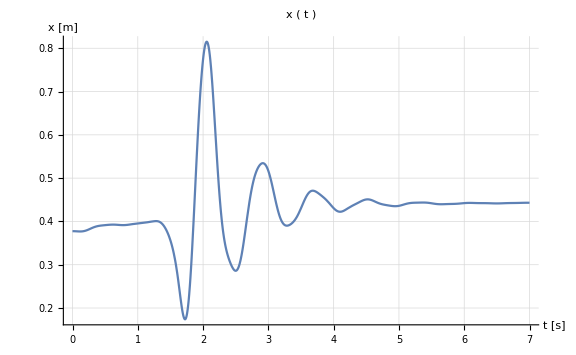
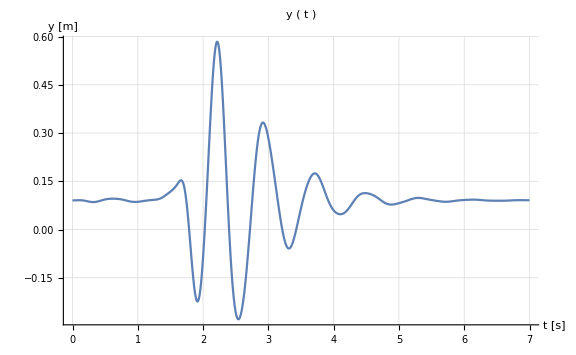
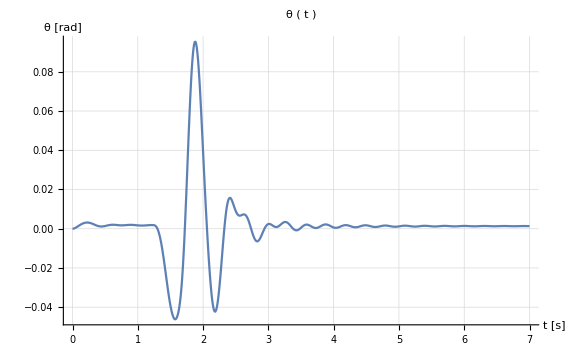

```mathematica
PAR = {m1->125, m2->15, g->9.8, L->1, l->0.2, k1->5600, k2->1344, c1->266, c2->60, udir[t_]->Piecewise[{{(dz[t]+Sin[angle[t]]),t≤7},{(dz[7]+Sin[angle[7]]),7≤t}}], udir'[t_]->Piecewise[{{(vz[t]+omega[t]),t≤7},{0,7≤t}}], uesq[t_]->Piecewise[{{(dz[t]-Sin[angle[t]]),t≤7},{(dz[7]-Sin[angle[7]]),7≤t}}], uesq'[t_]->Piecewise[{{(vz[t]-omega[t]),t≤7},{0,7≤t}}]};

eqs=(𝕖[t]/.PAR)/.Rule->Equal;
Module[{sol, ts=7}, 

sol= NDSolve[Join[eqs, {x[0]== (x[t]/.xeq), y[0]==(y[t]/.yeq), θ[0]==0, x'[0]==0, y'[0]==0, θ'[0]==0}],{x,y,θ},{t,0,ts}];
{

Plot[ Evaluate[(x[t]/.sol)],{t,0,ts}, PlotRange->All, ImageSize->Large,PlotLabel->"x ( t )", LabelStyle->"Subsubsection", GridLines->Automatic, AxesLabel->{"t [s]","x [m]"}],

Plot[ Evaluate[(y[t]/.sol)],{t,0,ts}, PlotRange->All, ImageSize->Large,PlotLabel->"y ( t )", LabelStyle->"Subsubsection",  GridLines->Automatic, AxesLabel->{"t [s]","y [m]"}],

Plot[ Evaluate[(θ[t]/.sol)],{t,0,ts}, PlotRange->All, ImageSize->Large,PlotLabel->"θ ( t )", LabelStyle->"Subsubsection",  GridLines->Automatic, AxesLabel->{"t [s]","θ [rad]"}]
}
]
```